## Допълнителни задачи по СНИ за упражнения 1 и 2

Зад. 0 В следните изрази са допуснати синтактични грешки. Поправете ги и изведете резултата от всеки от тях.
Забележка: Ако на пръв поглед не виждате грешката в някой от изразите, оценете стойността му (Shift + Enter). Това ще доведе до извеждане на съобщение за грешка, което може да ви помогне да откриете проблема.

```mathematica
cos[π/3]
```

```mathematica
p(x_):=x^7+E^x
```

```mathematica
Plot[E^x]
```

```mathematica
ListPlot[{0,0},{1,1},{2,√2},{3,√3},{4,2},{5,√5}]
```

```mathematica
list={1;2;3;4;8};
list[[5]]
```

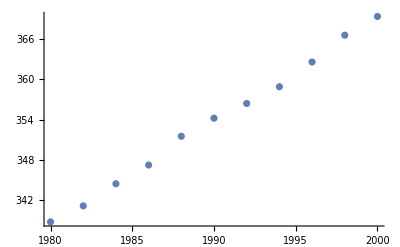
Зад. 1 Дадени са данни за изменението на нивото на въглеродния диоксид в атмосферата. На база на тези данни да се намери функция, която описва процесът. За целта да се използва вградената фукнция Fit. Графиката на получената функция да се начертае на една графика с данните.

data1={{1980,338.7},{1982,341.1},{1984,344.4},{1986,347.2},{1988,351.5},{1990,354.2},{1992,356.4},{1994,358.9},{1996,362.6},{1998,366.6},{2000,369.4}};
plot1=ListPlot[data1]
-Graphics-

Зад. 2 Основният математически труд на италианския математик Джироламо Кардано е свързан с решаването на полиномиални уравнения от трета и четвърта степен. Опитите му да намери аналитично решение на уравненията от трета степен водят до откриването на имагинерните числа, но те стават популярни доста по-късно, след публикации на други математици. 

Формулата на Кардано

x = (-q/2+√(q^2/4+p^3/27))^(1/3)+(-q/2-√(q^2/4+p^3/27))^(1/3)

 дава един от корените на кубично уравнение от вида
 
 x^3+p x+ q= 0.           (1)
 
Проверете дали кубичният полином (2 - √3+ x) (-4 + x )(2 + √3+ x) е от вида (1) (т.е приведете полинома в нормален вид и проверете дали старшият му коефициент е 1).  Ако да, пресметнете един от корените му по формулата на Кардано.

Зад. 3 При какви условия за аргумента x е в сила равенството ln(e^x) = x? Потвърдете предположението си като използвате подходяща фунцкия за опростяване на символни изрази.

Зад. 4 Дадена е графиката на функцията y=√x.
	(а) Начертайте графиките на  y=√x-2,  y = √(x-2),y= -√x, y=√-x с различни цветове на същата графика (PlotStyle);
 	(б) Начертайте графиката на оргиналната функция с плътна червена линия (PlotStyle->Thick);
	(в) Добавете легенда, описваща кой цвят, на коя функция отговаря (PlotLegends). 
Обяснете как посочените трансформации влияят върху поведението на функцията.
Забележка: С наклонен шрифт са дадени опциите на Plot, които са ви необходими за изпълнение на отделните подусловия.

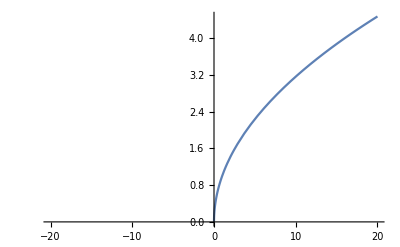

```mathematica
Plot[Sqrt[x],{x,-20,20}]
```